```mathematica
F1[n_,k_] := Sum[ (-1)^(a+1)/a Binomial[a,a],{a,1, Log[k,n]}]
F2[n_,k_, l_] := Sum[ (-1)^(a+b+1)/(a+b) Binomial[a+b,a] Binomial[b,b],{a,1, Log[k,n]},{b,1,Log[l,Floor[n/(k^a)]]}]
F3[n_,k_, l_,m_] := Sum[ (-1)^(a+b+c+1)/(a+b+c) Binomial[a+b+c,a] Binomial[b+c,b]Binomial[c,c],{a,1, Log[k,n]},{b,1,Log[l,Floor[n/(k^a)]]},{c,1,Log[m,Floor[n/( k^a l^b)]]}]
```

```mathematica
Table[{n=2^m,N[F1[n,2]],N[F2[n,2,3]],N[F3[n,2,3,4]]},{m,1,62}] // TableForm
```

2 | 1. | 0. | 0.
4 | 0.5 | 0. | 0.
8 | 0.833333 | -1. | 0.
16 | 0.583333 | 0. | 0.
32 | 0.783333 | 0. | 2.
64 | 0.616667 | -1.5 | -1.
128 | 0.759524 | 1.5 | -3.
256 | 0.634524 | -2.33333 | 8.
512 | 0.745635 | 1.16667 | -6.
1024 | 0.645635 | -0.333333 | -3.
2048 | 0.736544 | -2.75 | 14.
4096 | 0.653211 | 6.25 | -16.5
8192 | 0.730134 | -12.6167 | 9.
16384 | 0.658705 | 20.55 | -0.833333
32768 | 0.725372 | -34.2 | 9.16667
65536 | 0.662872 | 55.3 | -42.3333
131072 | 0.721695 | -92.1167 | 117.667
262144 | 0.66614 | 150.25 | -251.333
524288 | 0.718771 | -239.476 | 371.167
1048576 | 0.668771 | 360.69 | -298.5
2097152 | 0.71639 | -508.818 | 60.5
4194304 | 0.670936 | 652.349 | -146.
8388608 | 0.714414 | -725.435 | 996.483
16777216 | 0.672747 | 589.204 | -2017.18
33554432 | 0.712747 | 7.70437 | 1507.73
67108864 | 0.674286 | -1520.62 | 2068.23
134217728 | 0.711323 | 4730.96 | -8586.35
268435456 | 0.675609 | -10955.5 | 15969.1
536870912 | 0.710091 | 22318.6 | -22482.8
1073741824 | 0.676758 | -42127.4 | 31945.1
2147483648 | 0.709016 | 75295.1 | -57815.1
4294967296 | 0.677766 | -128814. | 120493.
8589934592 | 0.708069 | 212204. | -236775.
17179869184 | 0.678657 | -338019. | 402680.
34359738368 | 0.707229 | 522609. | -579903.
68719476736 | 0.679451 | -787975. | 729946.
137438953472 | 0.706478 | 1.16655×10^6 | -929368.
274877906944 | 0.680162 | -1.71305×10^6 | 1.45737×10^6
549755813888 | 0.705803 | 2.53137×10^6 | -2.65034×10^6
1099511627776 | 0.680803 | -3.83204×10^6 | 4.57908×10^6
2199023255552 | 0.705194 | 6.04775×10^6 | -7.0148×10^6
4398046511104 | 0.681384 | -1.00552×10^7 | 1.00849×10^7
8796093022208 | 0.70464 | 1.75835×10^7 | -1.554×10^7
17592186044416 | 0.681913 | -3.1939×10^7 | 2.82789×10^7
35184372088832 | 0.704135 | 5.92447×10^7 | -5.74291×10^7
70368744177664 | 0.682396 | -1.10484×10^8 | 1.15764×10^8
140737488355328 | 0.703672 | 2.04748×10^8 | -2.18145×10^8
281474976710656 | 0.682839 | -3.74166×10^8 | 3.85081×10^8
562949953421312 | 0.703247 | 6.71028×10^8 | -6.59132×10^8
1125899906842624 | 0.683247 | -1.17737×10^9 | 1.13206×10^9
2251799813685248 | 0.702855 | 2.01655×10^9 | -1.96546×10^9
4503599627370496 | 0.683624 | -3.36466×10^9 | 3.38078×10^9
9007199254740992 | 0.702492 | 5.45565×10^9 | -5.60347×10^9
18014398509481984 | 0.683974 | -8.56696×10^9 | 8.78448×10^9
36028797018963968 | 0.702155 | 1.29589×10^10 | -1.29819×10^10
72057594037927936 | 0.684298 | -1.8717×10^10 | 1.82466×10^10
144115188075855872 | 0.701842 | 2.54061×10^10 | -2.45664×10^10
288230376151711744 | 0.684601 | -3.13766×10^10 | 3.1057×10^10
576460752303423488 | 0.70155 | 3.24538×10^10 | -3.38318×10^10
1152921504606846976 | 0.684883 | -1.95621×10^10 | 2.25999×10^10
2305843009213693952 | 0.701277 | -2.54444×10^10 | 2.34529×10^10
4611686018427387904 | 0.685148 | 1.36921×10^11 | -1.40508×10^11

```mathematica
F1A[n_,k_] := Sum[ (-1)^(a+1)/a Binomial[a,a],{a,1, Infinity}]
F2A[n_,k_, l_] := Sum[ (-1)^(a+b+1)/(a+b) Binomial[a+b,a] Binomial[b,b],{a,1,Infinity},{b,1,Infinity}]
F3A[n_,k_, l_,m_] := Sum[ (-1)^(a+b+c+1)/(a+b+c) Binomial[a+b+c,a] Binomial[b+c,b]Binomial[c,c],{a,1, Infinity},{b,1,Infinity},{c,1,Infinity}]
F4A[n_,k_, l_,m_,o_] := Sum[ (-1)^(a+b+c+d+1)/(a+b+c+d) Binomial[a+b+c+d,a] Binomial[b+c+d,b]Binomial[c+d,c] Binomial[d,d],{a,1, Infinity},{b,1,Infinity},{c,1,Infinity},{d,1,Infinity}]
```

```mathematica
F4A[1000,2,3,4,5]
```

-6 Log[4]+Log[3645]

```mathematica
F1M[n_,k_] := Sum[ (-1)^(a) Binomial[a,a],{a,1, Log[k,n]}]
F2M[n_,k_, l_] := Sum[ (-1)^(a+b) Binomial[a+b,a] Binomial[b,b],{a,1, Log[k,n]},{b,1,Log[l,Floor[n/(k^a)]]}]
F3M[n_,k_, l_,m_] := Sum[ (-1)^(a+b+c) Binomial[a+b+c,a] Binomial[b+c,b]Binomial[c,c],{a,1, Log[k,n]},{b,1,Log[l,Floor[n/(k^a)]]},{c,1,Log[m,Floor[n/( k^a l^b)]]}]
```

```mathematica
Table[{n=2^m,N[F1M[n,2]],N[F2M[n,2,3]],N[F3M[n,2,3,4]]},{m,1,26}] // TableForm
```

2 | -1. | 0. | 0.
4 | 0. | 0. | 0.
8 | -1. | 2. | 0.
16 | 0. | -1. | 0.
32 | -1. | 0. | -6.
64 | 0. | 5. | 6.
128 | -1. | -9. | 10.
256 | 0. | 14. | -40.
512 | -1. | -13. | 48.
1024 | 0. | 6. | -6.
2048 | -1. | 15. | -79.
4096 | 0. | -55. | 151.
8192 | -1. | 123. | -156.
16384 | 0. | -231. | 116.
32768 | -1. | 409. | -140.
65536 | 0. | -714. | 398.
131072 | -1. | 1250. | -1290.
262144 | 0. | -2169. | 3324.
524288 | -1. | 3662. | -5811.
1048576 | 0. | -5893. | 6139.
2097152 | -1. | 8892. | -3403.
4194304 | 0. | -12309. | 3403.
8388608 | -1. | 15022. | -14514.
16777216 | 0. | -14407. | 33193.
33554432 | -1. | 5104. | -35043.
67108864 | 0. | 23168. | -15681.

```mathematica
F1Ma[n_,k_] := Sum[ (-1)^(a) Binomial[a,a],{a,1, Infinity}]
F2Ma[n_,k_, l_] := Sum[ (-1)^(a+b) Binomial[a+b,a] Binomial[b,b],{a,1,Infinity},{b,1,Log[l,Infinity]}]
F3Ma[n_,k_, l_,m_] := Sum[ (-1)^(a+b+c) Binomial[a+b+c,a] Binomial[b+c,b]Binomial[c,c],{a,1,Infinity},{b,1,Infinity},{c,1,Infinity}]
```

```mathematica
F1A[100,2]
F2A[100,2,3]
F3A[100,2,3,4]
```

Log[2]

-Log[4/3]

Log[32/27]

```mathematica
N[-Log[4/3]]
```

-0.287682

```mathematica
N[Log[32/27]]
```

0.169899

```mathematica
N[-6 Log[4]+Log[3645]]
```

-0.116655

```mathematica
Bin2[n_,k_] := Gamma[n+1]/(Gamma[k+1](Gamma[n-k+1]))
```

```mathematica
F1I[n_,k_] := Integrate[ (-1)^(a+1)/a Binomial[a,a],{a,1, Log[k,n]}]
F2I[n_,k_, l_] := Integrate[ (-1)^(a+b+1)/(a+b)Binomial[a+b,a]Binomial[b,b],{a,1, Log[k,n]},{b,1,Log[l,n/(k^a)]}]
F3I[n_,k_, l_,m_] := Integrate[ (-1)^(a+b+c+1)/(a+b+c)Binomial[a+b+c,a]Binomial[b+c,b]Binomial[c,c],{a,1, Log[k,n]},{b,1,Log[l,n/(k^a)]},{c,1,Log[m,n/( k^a l^b)]}]
```

```mathematica
Table[{n=2^m,N[F1I[n,2]],N[F2I[n,2,3]],N[F3I[n,2,3,4]]},{m,1,8}] // TableForm
```

$Aborted

```mathematica
Table[{n=2^m,N[F1I[n,2]],N[F2I[n,2,3]]},{m,1,12}] // TableForm
```

2 | 0. | 0.
4 | 0.0962286+0.433785 ⅈ | 0.308033+0.218235 ⅈ
8 | 0.0630477+0.177175 ⅈ | -0.344312-0.156246 ⅈ
16 | 0.0797846+0.359776 ⅈ | 0.613216-0.15015 ⅈ
32 | 0.0697067+0.217972 ⅈ | -0.172515+0.471386 ⅈ
64 | 0.0764373+0.333903 ⅈ | -0.105383-0.496747 ⅈ
128 | 0.0716248+0.235852 ⅈ | 0.675675+0.145189 ⅈ
256 | 0.0752365+0.320806 ⅈ | -0.504954+0.406999 ⅈ
512 | 0.0724262+0.24586 ⅈ | 0.335155-0.844099 ⅈ
1024 | 0.0746751+0.312908 ⅈ | 0.433607+0.98041 ⅈ
2048 | 0.0728347+0.252251 ⅈ | -0.841503-0.758871 ⅈ
4096 | -2.48491+0.30763 ⅈ | 1.51332+0.190476 ⅈ

```mathematica
Table[{n=2^m,N[F1[n,2]],N[F2[n,2,3]]+N[F1[n,6]],N[F3[n,2,3,4]]+N[F2[n,2,6]]+N[F2[n,3,4]]+N[F1[n,12]]},{m,1,62}] // TableForm
```

2 | 1. | 0. | 0.
4 | 0.5 | 0. | 0.
8 | 0.833333 | 0. | 0.
16 | 0.583333 | 1. | -1.
32 | 0.783333 | 1. | 2.
64 | 0.616667 | -1. | 0.
128 | 0.759524 | 2. | -1.
256 | 0.634524 | -1.5 | 4.5
512 | 0.745635 | 2. | -4.5
1024 | 0.645635 | 0.5 | -1.
2048 | 0.736544 | -2.16667 | 11.1667
4096 | 0.653211 | 6.83333 | -17.3333
8192 | 0.730134 | -11.8333 | 13.6667
16384 | 0.658705 | 21.3333 | 4.16667
32768 | 0.725372 | -33.4167 | -12.5833
65536 | 0.662872 | 55.9167 | -25.75
131072 | 0.721695 | -91.5 | 134.75
262144 | 0.66614 | 150.867 | -270.45
524288 | 0.718771 | -238.717 | 331.133
1048576 | 0.668771 | 361.45 | -247.7
2097152 | 0.71639 | -508.183 | 144.217
4194304 | 0.670936 | 652.983 | -345.95
8388608 | 0.714414 | -724.8 | 1098.57
16777216 | 0.672747 | 589.95 | -2020.6
33554432 | 0.712747 | 8.45 | 1803.23
67108864 | 0.674286 | -1519.97 | 1226.96
134217728 | 0.711323 | 4731.61 | -7568.04
268435456 | 0.675609 | -10954.9 | 15370.9
536870912 | 0.710091 | 22319.3 | -22088.3
1073741824 | 0.676758 | -42126.6 | 30292.9
2147483648 | 0.709016 | 75295.9 | -54161.6
4294967296 | 0.677766 | -128813. | 117842.
8589934592 | 0.708069 | 212205. | -238795.
17179869184 | 0.678657 | -338018. | 404581.
34359738368 | 0.707229 | 522610. | -572264.
68719476736 | 0.679451 | -787974. | 720238.
137438953472 | 0.706478 | 1.16655×10^6 | -938806.
274877906944 | 0.680162 | -1.71305×10^6 | 1.47565×10^6
549755813888 | 0.705803 | 2.53137×10^6 | -2.63198×10^6
1099511627776 | 0.680803 | -3.83204×10^6 | 4.52549×10^6
2199023255552 | 0.705194 | 6.04775×10^6 | -6.99008×10^6
4398046511104 | 0.681384 | -1.00552×10^7 | 1.00736×10^7
8796093022208 | 0.70464 | 1.75835×10^7 | -1.54024×10^7
17592186044416 | 0.681913 | -3.1939×10^7 | 2.79582×10^7
35184372088832 | 0.704135 | 5.92447×10^7 | -5.70044×10^7
70368744177664 | 0.682396 | -1.10484×10^8 | 1.15169×10^8
140737488355328 | 0.703672 | 2.04748×10^8 | -2.17171×10^8
281474976710656 | 0.682839 | -3.74166×10^8 | 3.83648×10^8
562949953421312 | 0.703247 | 6.71028×10^8 | -6.56916×10^8
1125899906842624 | 0.683247 | -1.17737×10^9 | 1.12835×10^9
2251799813685248 | 0.702855 | 2.01655×10^9 | -1.96073×10^9
4503599627370496 | 0.683624 | -3.36466×10^9 | 3.37643×10^9
9007199254740992 | 0.702492 | 5.45565×10^9 | -5.59696×10^9
18014398509481984 | 0.683974 | -8.56696×10^9 | 8.77029×10^9
36028797018963968 | 0.702155 | 1.29589×10^10 | -1.29641×10^10
72057594037927936 | 0.684298 | -1.8717×10^10 | 1.82372×10^10
144115188075855872 | 0.701842 | 2.54061×10^10 | -2.45564×10^10
288230376151711744 | 0.684601 | -3.13766×10^10 | 3.10167×10^10
576460752303423488 | 0.70155 | 3.24538×10^10 | -3.37714×10^10
1152921504606846976 | 0.684883 | -1.95621×10^10 | 2.25757×10^10
2305843009213693952 | 0.701277 | -2.54444×10^10 | 2.34527×10^10
4611686018427387904 | 0.685148 | 1.36921×10^11 | -1.40591×10^11

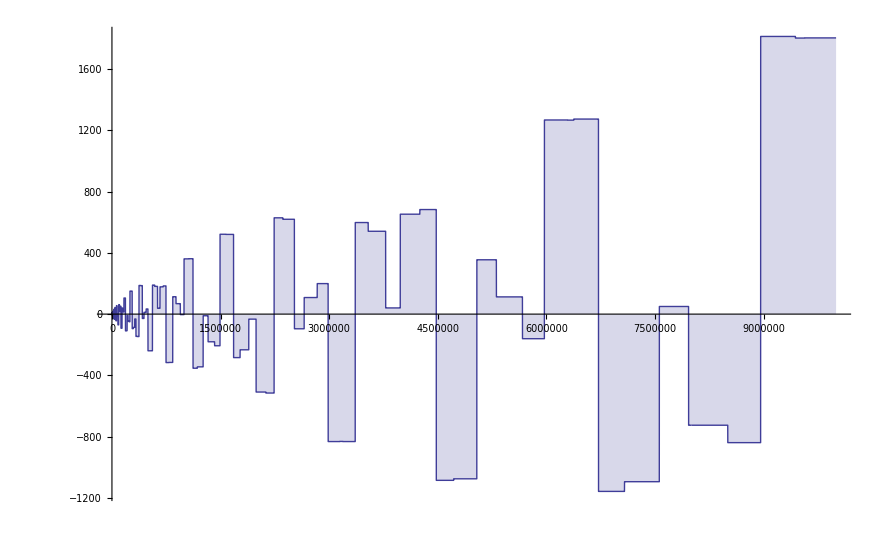

```mathematica
DiscretePlot[ F2[n,2,3],{n,1,10000000,1000}]
```

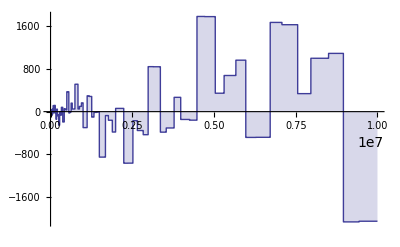

```mathematica
DiscretePlot[ F3[n,2,3,4],{n,1,10000000,1000}]
```

```mathematica
F2I[n,k, l]
```

∫_1^(Log[4611686018427387904]/Log[k]) ∫_1^(Log[4611686018427387904 k^-a]/Log[l]) ((-1)^(1+a+b) Binomial[a+b,a])/(a+b)ⅆbⅆa

```mathematica
Unprotect[Power];Power[0,0]=1;Protect[Power];
K[n_] := K[n]=FullSimplify[ MangoldtLambda[n]/Log[n]]
PP[n_,k_,a_]:=PP[n,k,a]=If[n<a^k,0,Sum[ K[a]^j  Binomial[k,j] PP[Floor[n/a^j], k-j, a+1], {j,0,k}]]
PP[n_,0,a_] := 1
```

```mathematica
PP[100,1,2]
```

428/15